## Lane-Emden code

The Lane-Emden equation (with the appropriate boundary conditions) is given by

```mathematica
LE[n_] := {1/ξ^2 D[(ξ^2 D[θa[ξ], ξ]), ξ] + θa[ξ]^n == 0, θa[0] == 1, θa'[0] == 0}
```

### Taylor Series Expansion

To get the taylor series expansion of the solution, we assume the form:

```mathematica
θa[ξ]=1+Sum[a[i] ξ^i,{i,4}]+O[ξ]^5
```

1+a[1] ξ+a[2] ξ^2+a[3] ξ^3+a[4] ξ^4+O[ξ]^5

Then we input it into the Lane-Emden equation to get an approximate solution.

```mathematica
LEseries[n_]:=θa[ξ]/.First@Solve[LogicalExpand[First[LE[n]/.θa[ξ]-> θa[ξ]]]]
```

```mathematica
LEseries[n]
```

1-ξ^2/6+(n ξ^4)/120+O[ξ]^5

```mathematica
system[n_, ξ0_] := {1/ξ^2 D[(ξ^2 D[θ[ξ], ξ]), ξ] + Sign[θ[ξ]] Abs[θ[ξ]]^n == 0, θ[ξ0] == Normal[LEseries[n]]/.ξ -> ξ0, θ'[ξ0] == D[Normal[LEseries[n]], ξ]/.ξ -> ξ0}
```

### Arrays

The numerical solutions for chosen polytropic indices are put in an array.

```mathematica
list = {3,4,4,5,6,7,10,15,32};
```

```mathematica
LEsoln = {};
Do[AppendTo[LEsoln,NDSolve[system[m/2,1/1000], θ[ξ], {ξ, 1/1000, list[[m]]}, WorkingPrecision -> 20]],{m,1,9}]
```

```mathematica
LEplots = {};
Do[AppendTo[LEplots,Plot[θ[ξ]/.{LEsoln[[m]]}, {ξ, 1/1000, list[[m]]}, PlotStyle -> {White,Thick}, Frame -> True, FrameLabel -> {Style["ξ", 16], Style["θ", 16]}]],{m,1,9}]
```

### Plot check

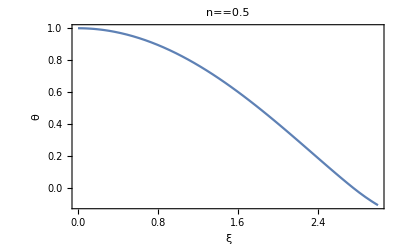

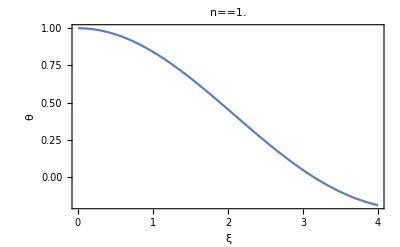

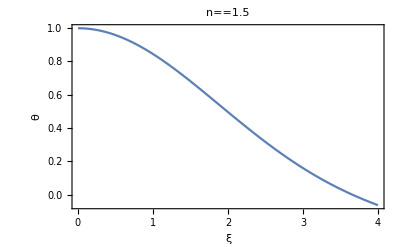

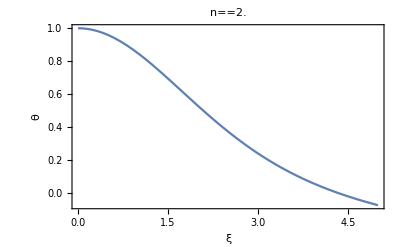

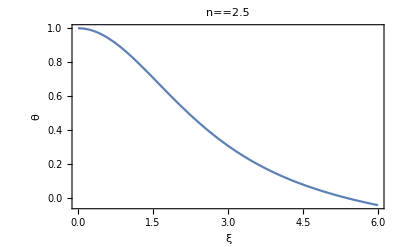

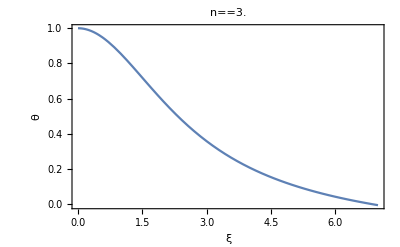

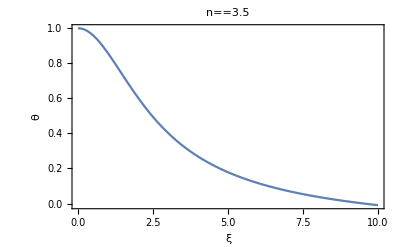

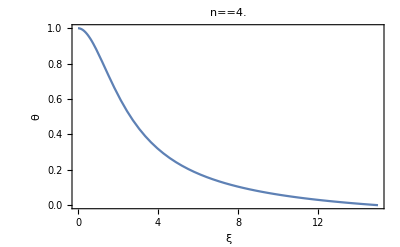

```mathematica
Do[Print[Plot[{θ[ξ]/.LEsoln[[m]]},{ξ,1/1000,
list[[m]]},PlotRange->All,Frame -> True, FrameLabel -> {Style["ξ", 16], Style["θ", 16]},PlotLabel-> n == N[(m/2)]]],{m,1,9}]
```